```mathematica
Integrate[k^2/(k^2-λ),{k,0,n},PrincipalValue->True,Assumptions->n>0&&0<Re[λ]<n^2&&λ==Re[λ]]
```

n+1/2 √λ Log[-1+(2 n)/(n+√λ)]

```mathematica
μ=0.4
```

0.4

```mathematica
NIntegrate[k^2/(k^2-μ^2)(NIntegrate[ν^2/(k^2-ν^2),{ν,0,k,1},Method->"PrincipalValue"]+k^2(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+(μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[ν^2/(μ^2-ν^2),{ν,0,μ,1},Method->"PrincipalValue"]+μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.251799

```mathematica
(A[μ]/.{n->1,α->1})^(-2)
```

0.251799+4.49956×10^-17 ⅈ

```mathematica
(μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))^2
```

0.0297333

```mathematica
Af[x_]:=A[x]/.{n->1,α->1}
(*Nummerical transform and inverse transform of f(x)=1*)
```

```mathematica
NIntegrate[Af[μ] k^2/(k^2-μ^2)(NIntegrate[Af[ν] ν^2/(k^2-ν^2),{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[ν] ν^2/(μ^2-ν^2),{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

```mathematica
(*Numerical transform and inverse transform of f(x)=x*)
μ
NIntegrate[Af[μ] k^2/(k^2-μ^2)(NIntegrate[Af[ν] ν^2/(k^2-ν^2)ν,{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2k(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[ν] ν^2/(μ^2-ν^2)ν,{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2μ(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.4

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {0.99988765950836122720448741196808128961492911912500858306884765625}. NIntegrate obtained 0.906371+2.95102×10^-16 ⅈ and 0.000445306 for the integral and error estimates.

0.399534-1.14822×10^-16 ⅈ

```mathematica
(*Numerical transform and inverse transform of f(x)=x^2*)
μ^2
NIntegrate[Af[μ] k^2/(k^2-μ^2)(NIntegrate[Af[ν] ν^2/(k^2-ν^2)ν^2,{ν,0,k,1},Method->"PrincipalValue"]+Af[k]k^2k^2(ArcTanh[k]/k+1/(4Pi*k^2))),{k,0,μ,1},Method->"PrincipalValue"]+Af[μ](μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))*(NIntegrate[Af[ν] ν^2/(μ^2-ν^2)ν^2,{ν,0,μ,1},Method->"PrincipalValue"]+Af[μ]μ^2μ^2(ArcTanh[μ]/μ+1/(4Pi*μ^2)))
```

0.16

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in k near {k} = {0.99994489573246928981623080773255551889633352402597665786743164062}. NIntegrate obtained 0.663551+2.12333×10^-16 ⅈ and 0.000131029 for the integral and error estimates.

0.159869-9.16378×10^-17 ⅈ

```mathematica
(*Determining the normalization Subscript[A, μ]*)
```

```mathematica
Clear[μ]
```

```mathematica
(*Transform 1/Subscript[A, ν]*)
```

```mathematica
Integrate[1/(k^2-μ^2)μ^2,{μ,0,n},PrincipalValue->True,Assumptions->k>0&&k^2<n^2&&n≥0]+k*ArcTanh[k/n]+α/(4Pi)
```

-n+α/(4 π)+k ArcTanh[k/n]-1/2 k Log[1-(2 k)/(k+n)]

```mathematica
(*-1/2 Log[1-(2 k)/(k+n)]=-1/2  Log[(n-k)/(n+k)]=-1/2  Log[(n-k)/(n+k)]=-1/2Log[1-k/n]+1/2 Log[1+k/n]*)
```

```mathematica
TrigToExp[ArcTanh[k/n]]
```

-1/2 Log[1-k/n]+1/2 Log[1+k/n]

```mathematica
FullSimplify[-n+α/(4 π)+k ArcTanh[k/n]+k ArcTanh[k/n]]
```

-n+α/(4 π)+2 k ArcTanh[k/n]

```mathematica
TrigToExp[-n+α/(4 π)+k (ArcTanh[k/n]+ArcTanh[k/n])]
```

-n+α/(4 π)-k Log[1-k/n]+k Log[1+k/n]

```mathematica
(*Inverse Transform divided by Subscript[A, μ]*)
```

```mathematica
(*First term*)
```

```mathematica
t1=Integrate[(-n+α/(4 π)-k Log[1-k/n]+k Log[1+k/n])k^2/(k^2-μ^2),{k,0,n},PrincipalValue->True,Assumptions->μ>0&&μ^2<n^2&&n≥0]
```

1/(4 π)(n α-α μ ArcTanh[μ/n]+2 ⅈ π^2 μ^2 Log[4]-2 π μ^2 Log[n] Log[-1+n^2/μ^2]+2 ⅈ π^2 μ^2 Log[n/(n-μ)]+2 π μ^2 Log[n] Log[n-μ]-4 π μ^2 Log[n] Log[μ]+2 ⅈ π^2 μ^2 Log[n/(n+μ)]+2 π μ^2 Log[n] Log[n+μ]+2 π μ^2 Log[n-μ] Log[n+μ]+2 π μ^2 Log[n+μ]^2+2 n π μ Log[(n+μ)/(n-μ)]-2 π μ^2 Log[n+μ] Log[n^2-μ^2]+2 π μ^2 PolyLog[2,(2 n)/(n-μ)]+2 π μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
(*Second term*)
```

```mathematica
t2=(μ*ArcTanh[μ/n]+α/(4Pi))*(-n+α/(4 π)+2 μ ArcTanh[μ/n]);
```

```mathematica
(*Total inverse transform*)
```

```mathematica
t1+t2
```

(α/(4 π)+μ ArcTanh[μ/n]) (-n+α/(4 π)+2 μ ArcTanh[μ/n])+1/(4 π)(n α-α μ ArcTanh[μ/n]+2 ⅈ π^2 μ^2 Log[4]-2 π μ^2 Log[n] Log[-1+n^2/μ^2]+2 ⅈ π^2 μ^2 Log[n/(n-μ)]+2 π μ^2 Log[n] Log[n-μ]-4 π μ^2 Log[n] Log[μ]+2 ⅈ π^2 μ^2 Log[n/(n+μ)]+2 π μ^2 Log[n] Log[n+μ]+2 π μ^2 Log[n-μ] Log[n+μ]+2 π μ^2 Log[n+μ]^2+2 n π μ Log[(n+μ)/(n-μ)]-2 π μ^2 Log[n+μ] Log[n^2-μ^2]+2 π μ^2 PolyLog[2,(2 n)/(n-μ)]+2 π μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
%//Simplify
```

1/16 (α^2/π^2-16 n μ ArcTanh[μ/n]+(8 α μ ArcTanh[μ/n])/π+32 μ^2 ArcTanh[μ/n]^2+8 ⅈ π μ^2 Log[4]-8 μ^2 Log[n] Log[-1+n^2/μ^2]+8 ⅈ π μ^2 Log[n/(n-μ)]+8 μ^2 Log[n] Log[n-μ]-16 μ^2 Log[n] Log[μ]+8 ⅈ π μ^2 Log[n/(n+μ)]+8 μ^2 Log[n] Log[n+μ]+8 μ^2 Log[n-μ] Log[n+μ]+8 μ^2 Log[n+μ]^2+8 n μ Log[(n+μ)/(n-μ)]-8 μ^2 Log[n+μ] Log[n^2-μ^2]+8 μ^2 PolyLog[2,(2 n)/(n-μ)]+8 μ^2 PolyLog[2,(2 n)/(n+μ)])

```mathematica
%//Expand
```

α^2/(16 π^2)-n μ ArcTanh[μ/n]+(α μ ArcTanh[μ/n])/(2 π)+2 μ^2 ArcTanh[μ/n]^2+1/2 ⅈ π μ^2 Log[4]-1/2 μ^2 Log[n] Log[-1+n^2/μ^2]+1/2 ⅈ π μ^2 Log[n/(n-μ)]+1/2 μ^2 Log[n] Log[n-μ]-μ^2 Log[n] Log[μ]+1/2 ⅈ π μ^2 Log[n/(n+μ)]+1/2 μ^2 Log[n] Log[n+μ]+1/2 μ^2 Log[n-μ] Log[n+μ]+1/2 μ^2 Log[n+μ]^2+1/2 n μ Log[(n+μ)/(n-μ)]-1/2 μ^2 Log[n+μ] Log[n^2-μ^2]+1/2 μ^2 PolyLog[2,(2 n)/(n-μ)]+1/2 μ^2 PolyLog[2,(2 n)/(n+μ)]

```mathematica
AA=%//FullSimplify
```

1/(16 π^2)(α^2+8 π μ ((-2 n π+α) ArcTanh[μ/n]+4 π μ ArcTanh[μ/n]^2+π (ⅈ π μ (Log[(4 n)/(n-μ)]+Log[n/(n+μ)])+μ Log[n] (-Log[-1+n^2/μ^2]+Log[n-μ]-2 Log[μ]+Log[n+μ])+n Log[(n+μ)/(n-μ)]+μ Log[n+μ] (Log[n-μ]+Log[n+μ]-Log[n^2-μ^2])))+8 π^2 μ^2 (PolyLog[2,(2 n)/(n-μ)]+PolyLog[2,(2 n)/(n+μ)]))

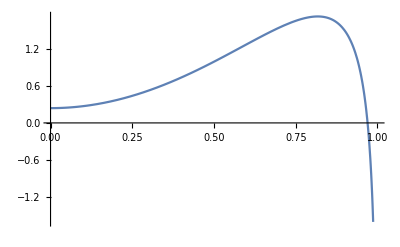

```mathematica
Plot[%/.{n->1,α->3},{μ,0,1}]
```

```mathematica
A[μ_]:=(AA)^(-1/2)
```

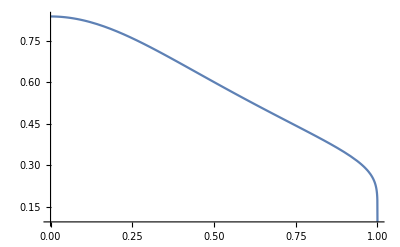

```mathematica
Plot[A[μ]/.{α->15,n->1},{μ,0,1}]
```